```mathematica
ϕ=(1+√5)/2;
```

```mathematica
basicRays={{0,0,2,2},{0,0,2,-2},{1,1,1,√5},{1,1,1,-√5},{1,1,-1,-√5},{1,1,-1,√5},{ϕ,ϕ,ϕ,ϕ^-2},{ϕ,ϕ,ϕ,-ϕ^-2},{ϕ,ϕ,-ϕ,-ϕ^-2},{ϕ,ϕ,-ϕ,ϕ^-2},{ϕ^-1,ϕ^-1,ϕ^-1,ϕ^2},{ϕ^-1,ϕ^-1,ϕ^-1,-ϕ^2},{ϕ^-1,ϕ^-1,-ϕ^-1,-ϕ^2},{ϕ^-1,ϕ^-1,-ϕ^-1,ϕ^2}};
```

```mathematica
allPerms=Union@@Permutations/@basicRays;
```

```mathematica
evenRays={0,ϕ^-2
```

```mathematica
allPerms
```

```mathematica
(*alternative approach*)
```

```mathematica
cellV[1]={1,0,0,0};cellV[2]={0,1,0,0};cellV[3]={0,0,1,0};cellV[4]={0,0,0,1};
```

```mathematica
cellList[1]={cellV[1],cellV[2],cellV[3],cellV[4]};
```

```mathematica
τ=(1+√5)/2;
U=1/2({{1, 1, 1, -1}, {1, 1, -1, 1}, {1, -1, 1, 1}, {1, -1, -1, -1}});
V=1/2({{τ, 0, -1, 1/τ}, {0, τ, -1/τ, -1}, {1, 1/τ, τ, 0}, {-1/τ, 1, 0, τ}});
W=1/2({{1/τ, -τ, 0, 1}, {τ, 1/τ, 1, 0}, {0, -1, 1/τ, -τ}, {-1, 0, τ, 1/τ}});
```

```mathematica
Simplify/@{MatrixPower[U,3],MatrixPower[V,5],MatrixPower[W,5]}
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}}

```mathematica
cellList[2]=cellList[1] ∪ (Dot[U,#]&/@cellList[1])∪(Dot[MatrixPower[U,2],#]&/@cellList[1]);
```

```mathematica
cellList[3]=Simplify/@Union@@NestList[Dot[V,#]&/@#&,cellList[2],4];
```

```mathematica
cellList[4]=Simplify/@Union@@NestList[Dot[W,#]&/@#&,cellList[2],4];
```

```mathematica
Length[cellList[3]]
```

60

```mathematica
bigTable=Flatten[Table[Simplify[MatrixPower[W,n].MatrixPower[V,m].MatrixPower[U,l].cellV[i]],{i,1,4},{l,0,2},{m,0,4},{n,0,4}],3];
```

```mathematica
Length[bigTable]
```

300

```mathematica
numericalOrthogonalityGraph[statelist_]:=AdjacencyGraph[If[Abs[#]<2$MachineEpsilon,1,0]&/@#&/@Outer[Dot,statelist,statelist,1]]
```

```mathematica
orthogonalityGraph[statelist_]:=AdjacencyGraph[Simplify[Outer[Dot,statelist,statelist,1]]/.{0->1,x_/;x≠0->0}]
```

```mathematica
cellGraphN=numericalOrthogonalityGraph[bigTableW];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/4-1/(2 (1+√5))+1/8 (1+√5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4+1/8 (-1-√5)+1/8 (-1+√5).

General::stop: Further output of N::meprec will be suppressed during this calculation.

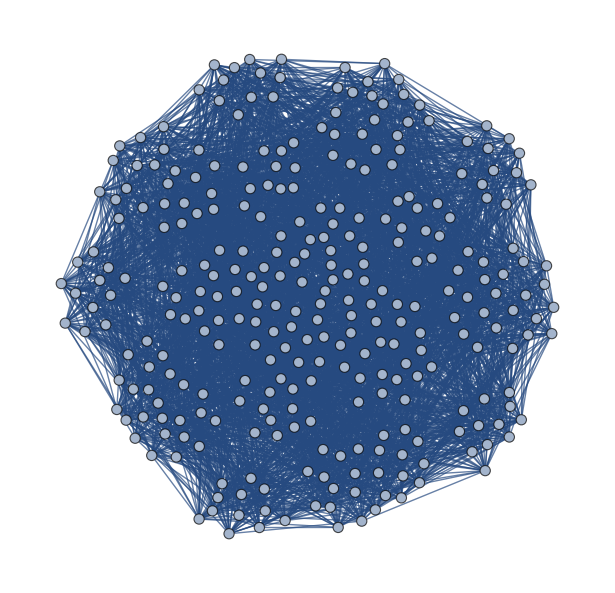

```mathematica
cellGraph=orthogonalityGraph[bigTableW]
```

```mathematica
2$MachineEpsilon
```

4.44089×10^-16

```mathematica
cellGraph==cellGraphN
```

True

```mathematica
Parallelize[{FindIndependentVertexSet[cellGraph],FindIndependentVertexSet[cellGraphN]}]
```

Parallelize[FindIndependentVertexSet[cellGraph],{{1,6,12,15,20,24,27,32,33,45,49,54,57,72,74,80,84,86,92,93,100,102,105,112,114,120,122,125,132,134,146,150,155,160,162,167,172,173,180,182,185,190,194,198,202,207,210,215,219,221,227,233,241,246,250,255,258,262,267,279,281,285,289,293,297}}]

```mathematica
FindIndependentVertexSet[cellGraph]
```

{{1,6,12,15,20,24,27,32,33,45,49,54,57,72,74,80,84,86,92,93,100,102,105,112,114,120,122,125,132,134,146,150,155,160,162,167,172,173,180,182,185,190,194,198,202,207,210,215,219,221,227,233,241,246,250,255,258,262,267,279,281,285,289,293,297}}

```mathematica
Length@{1,6,12,15,20,24,27,32,33,45,49,54,57,72,74,80,84,86,92,93,100,102,105,112,114,120,122,125,132,134,146,150,155,160,162,167,172,173,180,182,185,190,194,198,202,207,210,215,219,221,227,233,241,246,250,255,258,262,267,279,281,285,289,293,297}
```

65

```mathematica
bigTable[[60*3]]
```

```mathematica
bigTableW=Flatten[Table[Simplify[MatrixPower[W,n].MatrixPower[V,m].MatrixPower[U,l].cellV[i]],{n,0,4},{m,0,4},{l,0,2},{i,1,4}],3];
```

```mathematica
bigTableW[[60*1+12*2+4*1+1]]
```

{(√5)/4,1/4,1/4,3/4}

```mathematica
Simplify[MatrixPower[W,1].MatrixPower[V,2].MatrixPower[U,1].cellV[1]]
```

{(√5)/4,1/4,1/4,3/4}

```mathematica
Simplify[1/4+1/8 (-1-√5)+1/8 (-1+√5)]
```

0

```mathematica
contexts=Sort[Sort/@FindClique[cellGraph,{4},All]];
```

```mathematica
Length@contexts
```

675

```mathematica
unsolvedContexts[contexts_,oneAssignment_]:=Select[contexts/.Thread[Unevaluated[oneAssignment->Nothing]],Length[#]==Max[Length/@contexts]&]
```

```mathematica
usc=unsolvedContexts[contexts,{1,6,12,15,20,24,27,32,33,45,49,54,57,72,74,80,84,86,92,93,100,102,105,112,114,120,122,125,132,134,146,150,155,160,162,167,172,173,180,182,185,190,194,198,202,207,210,215,219,221,227,233,241,246,250,255,258,262,267,279,281,285,289,293,297}];
```

```mathematica
fullTable=Join[bigTableW,-bigTableW]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2},{1/2,-1/2,1/2,-1/2},{-1/2,1/2,1/2,-1/2},585,{1/8 (5-√5),1/8 (-1+√5),1/8 (-3-√5),1/8 (3+√5)},{1/8 (1-√5),1/8 (-1-3 √5),1/8 (1-√5),1/8 (-1+√5)},{1/8 (3+√5),1/8 (1-√5),1/8 (-5+√5),1/8 (-3-√5)},{3/4,-(√5)/4,-1/4,1/4},{1/4,(√5)/4,1/4,3/4},{-1/4,-(√5)/4,3/4,1/4},{-(√5)/4,-1/4,-(√5)/4,(√5)/4}}
 |  |  |  |

```mathematica
RotationMatrix[θ,{{1,0,0,0},{0,1,0,0}}]
```

{{Cos[θ],-Sin[θ],0,0},{Sin[θ],Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Manipulate[ListPointPlot3D[Drop[#,-1]&/@(RotationMatrix[θ,{{1/√2,0,1/√2,0},{0,1/√2,0,1/√2}}].#&/@fullTable),BoxRatios->{1,1,1}],{θ,0,2π}]
```

ListPointPlot3D::arrayerr: fullTable must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

```mathematica
greedySolve[usc]
```

32